```mathematica
Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-speaking-masks/Std01.m142"]]//Quiet;
```

C:\Users\mona_\AppData\Local\Temp\Std01-b85d182f-eac3-4edd-9ee8-bf1ad16b2928.m142        23.7.2026 10:42:12.    (135530 Bytes)

```mathematica
Clear[G,h,M,S]
```

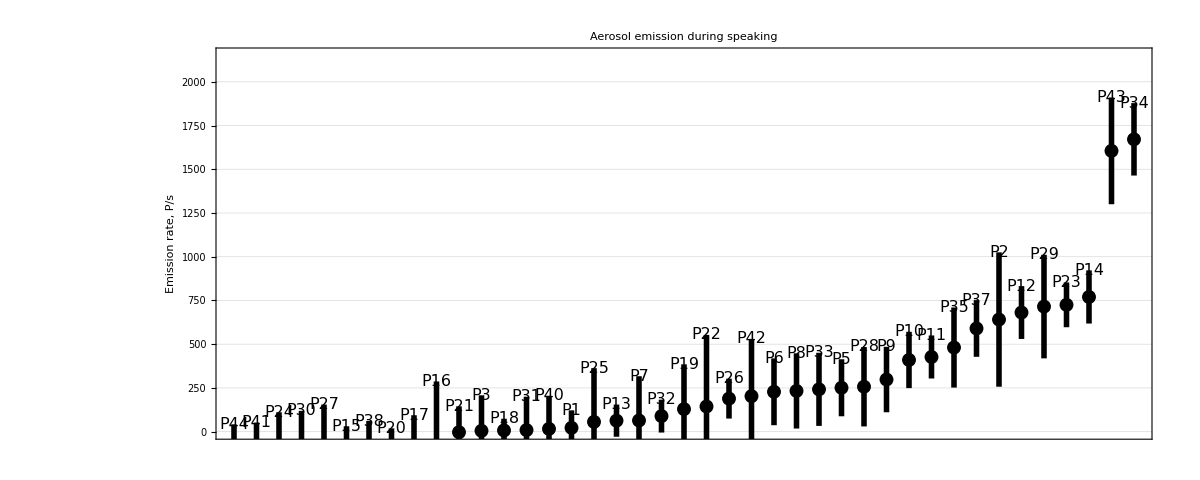

{NormalDistribution[-306.,348.],NormalDistribution[-260.,312.],NormalDistribution[-245.,356.],NormalDistribution[-175.,294.],NormalDistribution[-164.,319.],NormalDistribution[-144.,175.],NormalDistribution[-137.,198.],NormalDistribution[-121.,140.],NormalDistribution[-80.,174.],NormalDistribution[-79.,366.],NormalDistribution[-3.,148.],NormalDistribution[5.,203.],NormalDistribution[7.,67.],NormalDistribution[9.,191.],NormalDistribution[16.,189.],NormalDistribution[22.,100.],NormalDistribution[56.,307.],NormalDistribution[63.,92.],NormalDistribution[64.,253.],NormalDistribution[89.,94.],NormalDistribution[129.,256.],NormalDistribution[144.,409.],NormalDistribution[189.,114.],NormalDistribution[203.,327.],NormalDistribution[228.,191.],NormalDistribution[233.,215.],NormalDistribution[242.,209.],NormalDistribution[251.,163.],NormalDistribution[257.,227.],NormalDistribution[298.,187.],NormalDistribution[410.,161.],NormalDistribution[427.,123.],NormalDistribution[481.,229.],NormalDistribution[590.,162.],NormalDistribution[641.,384.],NormalDistribution[681.,151.],NormalDistribution[715.,296.],NormalDistribution[725.,128.],NormalDistribution[770.,152.],NormalDistribution[1605.,305.],NormalDistribution[1671.,207.]}

```mathematica
{S,G,h} = Get[URLDownload[F="https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-speaking-masks/Fig/TaskPlots/P-s/Speaking.dat"]];
G
S
```

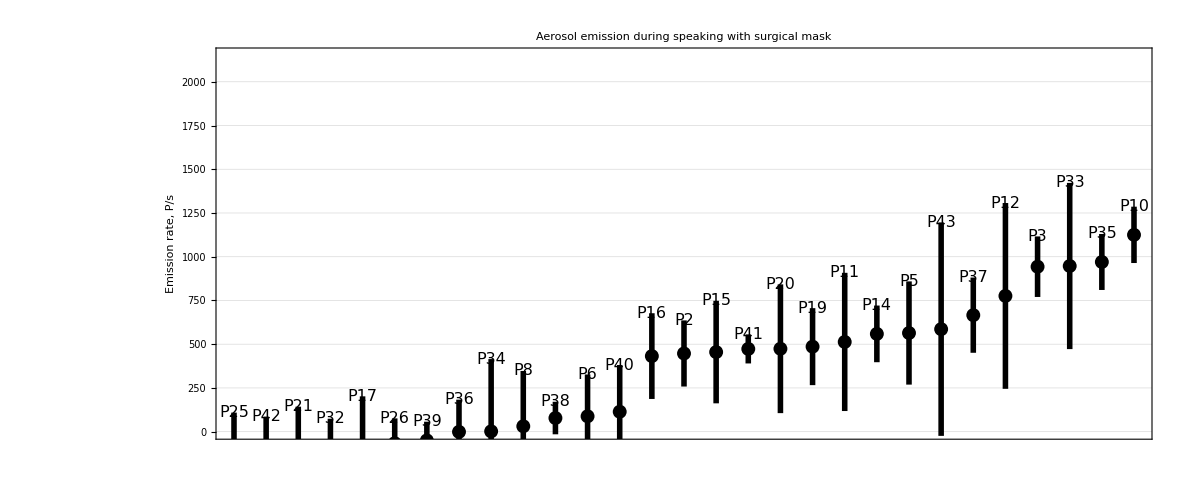

{NormalDistribution[-164.,273.],NormalDistribution[-163.,249.],NormalDistribution[-136.,279.],NormalDistribution[-122.,196.],NormalDistribution[-89.,291.],NormalDistribution[-66.,142.],NormalDistribution[-50.,107.],NormalDistribution[-1.,184.],NormalDistribution[2.,413.],NormalDistribution[31.,316.],NormalDistribution[78.,93.],NormalDistribution[88.,239.],NormalDistribution[114.,267.],NormalDistribution[432.,245.],NormalDistribution[447.,189.],NormalDistribution[455.,293.],NormalDistribution[473.,83.],NormalDistribution[474.,368.],NormalDistribution[486.,220.],NormalDistribution[513.,395.],NormalDistribution[559.,162.],NormalDistribution[564.,295.],NormalDistribution[586.,610.],NormalDistribution[666.,215.],NormalDistribution[776.,531.],NormalDistribution[943.,173.],NormalDistribution[947.,475.],NormalDistribution[970.,160.],NormalDistribution[1125.,161.]}

```mathematica
{M,G,h} = Get[URLDownload[F="https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-speaking-masks/Fig/TaskPlots/P-s/Speaking%20With%20Surgical%20Mask.dat"]];
G
M
```

```mathematica
M = First/@M
S = First/@S
```

{-164.,-163.,-136.,-122.,-89.,-66.,-50.,-1.,2.,31.,78.,88.,114.,432.,447.,455.,473.,474.,486.,513.,559.,564.,586.,666.,776.,943.,947.,970.,1125.}

{-306.,-260.,-245.,-175.,-164.,-144.,-137.,-121.,-80.,-79.,-3.,5.,7.,9.,16.,22.,56.,63.,64.,89.,129.,144.,189.,203.,228.,233.,242.,251.,257.,298.,410.,427.,481.,590.,641.,681.,715.,725.,770.,1605.,1671.}

```mathematica
(*    negative fit curve slopes are not physical plausible and need to be corrected to zero    *)

M = Select[M,(#>0.)&]
S = Select[S,(#>0.)&]
```

{2.,31.,78.,88.,114.,432.,447.,455.,473.,474.,486.,513.,559.,564.,586.,666.,776.,943.,947.,970.,1125.}

{5.,7.,9.,16.,22.,56.,63.,64.,89.,129.,144.,189.,203.,228.,233.,242.,251.,257.,298.,410.,427.,481.,590.,641.,681.,715.,725.,770.,1605.,1671.}

```mathematica
(*    emission rates below 25 P/s produce respiratory particle concentrations too low to distinguish them from background signal    *)

M = Select[M,(#>=25.)&]
S = Select[S,(#>=25.)&]
```

{31.,78.,88.,114.,432.,447.,455.,473.,474.,486.,513.,559.,564.,586.,666.,776.,943.,947.,970.,1125.}

{56.,63.,64.,89.,129.,144.,189.,203.,228.,233.,242.,251.,257.,298.,410.,427.,481.,590.,641.,681.,715.,725.,770.,1605.,1671.}

```mathematica
S = Select[S,(#<1500.)&]                                           (*    ohne P34 und P43    *)
```

{56.,63.,64.,89.,129.,144.,189.,203.,228.,233.,242.,251.,257.,298.,410.,427.,481.,590.,641.,681.,715.,725.,770.}

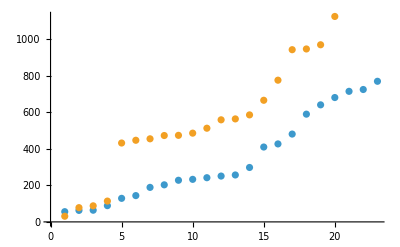

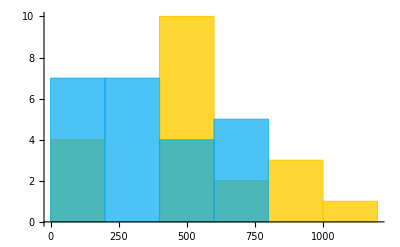

```mathematica
ListPlot[{S,M}]                       (*    ohne Maske: blau, mit Maske: orange    *)
Histogram[{M,S}]                       (*    ohne Maske: blau, mit Maske: orange    *)
```

```mathematica
-Graphics-;


Clear[MannWhitneyUStat]


MannWhitneyUStat[X_,Y_] := Module[{k,n1,n2,U,Z},                                                           (*    https://de.wikipedia.org/wiki/Wilcoxon-Mann-Whitney-Test    *)
{n2,n1} = Sort[{Length[X],Length[Y]}];                                                                             (*    Zweiseitiger Test zum Signifikanzniveau α = 5%               *)
U = Min[
Total/@Total/@{
Outer[If[#2<#1,1,If[#2==#1,1/2,0]]&,X,Y],
Outer[If[#2<#1,1,If[#2==#1,1/2,0]]&,Y,X]}];
If[(n1>40)||(n2>20),
Return[{
n1,n2,U,
Z = (U-n1 n2/2)/√(n1 n2(n1+n2+1)/12);
N[Z],
Abs[Z]>1.9599639845400538                                                                                                     (*    Quantile[NormalDistribution[0,1],0.975]    *)
}]];
{n1,n2,U,k={
{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,0,0},{Null,Null,Null,Null,Null,Null,Null,0,0,0,0,1,1,1,1,1,2,2,2,2,3,3,3,3,3,4,4,4,4,5,5,5,5,5,6,6,6,6,7,7},{Null,Null,Null,Null,0,1,1,2,2,3,3,4,4,5,5,6,6,7,7,8,8,9,9,10,10,11,11,12,13,13,14,14,15,15,16,16,17,17,18,18},{Null,Null,Null,0,1,2,3,4,4,5,6,7,8,9,10,11,11,12,13,14,15,16,17,17,18,19,20,21,22,23,24,24,25,26,27,28,29,30,31,31},{Null,Null,Null,Null,2,3,5,6,7,8,9,11,12,13,14,15,17,18,19,20,22,23,24,25,27,28,29,30,32,33,34,35,37,38,39,40,41,43,44,45},{Null,Null,Null,Null,Null,5,6,8,10,11,13,14,16,17,19,21,22,24,25,27,29,30,32,33,35,37,38,40,42,43,45,46,48,50,51,53,55,56,58,59},{Null,Null,Null,Null,Null,Null,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74},{Null,Null,Null,Null,Null,Null,Null,13,15,17,19,22,24,26,29,31,34,36,38,41,43,45,48,50,53,55,57,60,62,65,67,69,72,74,77,79,81,84,86,89},{Null,Null,Null,Null,Null,Null,Null,Null,17,20,23,26,28,31,34,37,39,42,45,48,50,53,56,59,62,64,67,70,73,76,78,81,84,87,89,92,95,98,101,103},{Null,Null,Null,Null,Null,Null,Null,Null,Null,23,26,29,33,36,39,42,45,48,52,55,58,61,64,67,71,74,77,80,83,87,90,93,96,99,103,106,109,112,115,119},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,30,33,37,40,44,47,51,55,58,62,65,69,73,76,80,83,87,90,94,98,101,105,108,112,116,119,123,127,130,134},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,37,41,45,49,53,57,61,65,69,73,77,81,85,89,93,97,101,105,109,113,117,121,125,129,133,137,141,145,149},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,45,50,54,59,63,67,72,76,80,85,89,94,98,102,107,111,116,120,125,129,133,138,142,147,151,156,160,165},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,55,59,64,69,74,78,83,88,93,98,102,107,112,117,122,127,131,136,141,146,151,156,161,165,170,175,180},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,64,70,75,80,85,90,96,101,106,111,117,122,127,132,138,143,148,153,159,164,169,174,180,185,190,196},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,75,81,86,92,98,103,109,115,120,126,132,137,143,149,154,160,166,171,177,183,188,194,200,206,211},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,87,93,99,105,111,117,123,129,135,141,147,154,160,166,172,178,184,190,196,202,209,215,221,227},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,99,106,112,119,125,132,138,145,151,158,164,171,177,184,190,197,203,210,216,223,230,236,243},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,113,119,126,133,140,147,154,161,168,175,182,189,196,203,210,217,224,231,238,245,252,258},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,127,134,141,149,156,163,171,178,186,193,200,208,215,222,230,237,245,252,259,267,274}
}[[n2,n1]],
If[IntegerQ[k],U<k,False]}];
```

```mathematica
MannWhitneyUStat[S,M]                                                              (*    von Oliver    *)
MannWhitneyUStat[M,S]
```

MannWhitneyUStat[{56.,63.,64.,89.,129.,144.,189.,203.,228.,233.,242.,251.,257.,298.,410.,427.,481.,590.,641.,681.,715.,725.,770.},{31.,78.,88.,114.,432.,447.,455.,473.,474.,486.,513.,559.,564.,586.,666.,776.,943.,947.,970.,1125.}]

MannWhitneyUStat[{31.,78.,88.,114.,432.,447.,455.,473.,474.,486.,513.,559.,564.,586.,666.,776.,943.,947.,970.,1125.},{56.,63.,64.,89.,129.,144.,189.,203.,228.,233.,242.,251.,257.,298.,410.,427.,481.,590.,641.,681.,715.,725.,770.}]

```mathematica
α = 0.05;
```

```mathematica
MannWhitneyTest[{S,M},0,"TestData",SignificanceLevel->α]                            (*    Mathematica built-in    *)
MannWhitneyTest[{M,S},0,"TestData",SignificanceLevel->α]
```

{151.,0.0528966}

{151.,0.0559513}

```mathematica
MannWhitneyTest[{S,M},0,"ShortTestConclusion",SignificanceLevel->α]                            (*    Mathematica built-in    *)
MannWhitneyTest[{M,S},0,"ShortTestConclusion",SignificanceLevel->α]
```

Do not reject

Do not reject